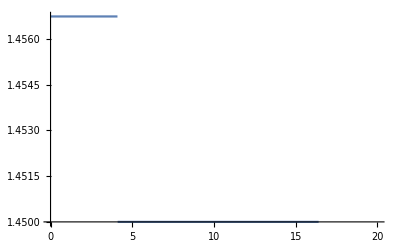

```mathematica
(*1*)
Clear["Global`*"]

dCore=8.2;
NA=0.14;
λ=1.55;
nMat=1.45;
β0=2Pi nMat/λ;
nMax=Sqrt[nMat^2+NA^2];

CalcWindow=20;(*mkm*)
N0=Round[(Sqrt[2]β0*CalcWindow)/(2π)]+1;(*из параксиального приближения(+1 для того, чтобы число было нечетным)*)
ϕmax=Pi/10;(*максимальный набег фазы за один шаг*)
h=Min[{N[ϕmax/((Pi/CalcWindow*(N0-1)/2)^2/β0)],
N[ϕmax/((β0/nMat*(NA))^2/2/β0)]}];(*определяем шаг так, чтобы операторы FourierOp и SpatialOp меняли фазу за шаг h максимум на ϕmax*)
n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2],0≤r<dCore/2},{nMat,dCore/2≤r<2dCore},{Sqrt[nMat^2-imn*I],2dCore≤r}}];
Plot[Re[n[r]],{r,0,CalcWindow}]
Clear[imn]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

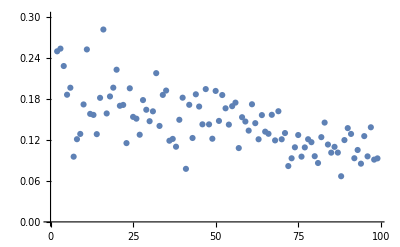

```mathematica
Clear[finξ];
finξ={};
For[
i=1,i≤11,i++,
imn=0.0005+i*0.001;
If[i==11,{imnopt=0.0005+Position[finξ,Min[finξ]][[1,1]]*0.001;imn=imnopt;}];
n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2],0≤r<dCore/2},{nMat,dCore/2≤r<2dCore},{Sqrt[nMat^2-imn*I],2dCore≤r}}];
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I/β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];

Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
PrevBeam=Abs[Beam[[(N0+1)/2]]];
CurBeam=Abs[Beam[[(N0+1)/2]]];
Clear[par];
CritPar=0.01;
par={};
L=10000 h;
RepPoint=100;(*промежуток, между которыми сравниваются решения, в величинах h*)
Monitor[
For[ξ=0.5h,ξ<L,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];
If[Mod[Ceiling[ξ/h-0.5],RepPoint]==0&&ξ>50h,
{
PrevBeam=CurBeam;
CurBeam=Abs[Beam[[(N0+1)/2]]];
par=AppendTo[par,NIntegrate[Abs[Interpolation[PrevBeam,InterpolationOrder->3][x]-Interpolation[CurBeam,InterpolationOrder->3][x]],{x,1,N0}]/NIntegrate[Interpolation[PrevBeam,InterpolationOrder->3][x],{x,1,N0}]];
If[Dimensions[par][[1]]>1,
If[par[[-1]]<CritPar&&par[[-2]]<CritPar,Break[]]];
}
];
],{ξ,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{ {-CalcWindow,CalcWindow},All},ImageSize->Large]}];
AppendTo[finξ,ξ];
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];
]
ListPlot[par]
```

```mathematica
(*рассчет для конкретного значения imn*)
imn=0.0055;
n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2],0≤r<dCore/2},{nMat,dCore/2≤r<2dCore},{Sqrt[nMat^2-imn*I],2dCore≤r}}];
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I/β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];

Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
PrevBeam=Abs[Beam[[(N0+1)/2]]];
CurBeam=Abs[Beam[[(N0+1)/2]]];
Clear[par];
CritPar=0.01;
par={};
L=10000 h;
RepPoint=100;(*промежуток, между которыми сравниваются решения, в величинах h*)
Monitor[
For[ξ=0.5h,ξ<L,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];
If[Mod[Ceiling[ξ/h-0.5],RepPoint]==0&&ξ>50h,
{
PrevBeam=CurBeam;
CurBeam=Abs[Beam[[(N0+1)/2]]];
par=AppendTo[par,NIntegrate[Abs[Interpolation[PrevBeam,InterpolationOrder->3][x]-Interpolation[CurBeam,InterpolationOrder->3][x]],{x,1,N0}]/NIntegrate[Interpolation[PrevBeam,InterpolationOrder->3][x],{x,1,N0}]];
If[Dimensions[par][[1]]>1,
If[par[[-1]]<CritPar&&par[[-2]]<CritPar,Break[]]];
}
];
],{ξ,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{ {-CalcWindow,CalcWindow},All},ImageSize->Large]}];
AppendTo[finξ,ξ];
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

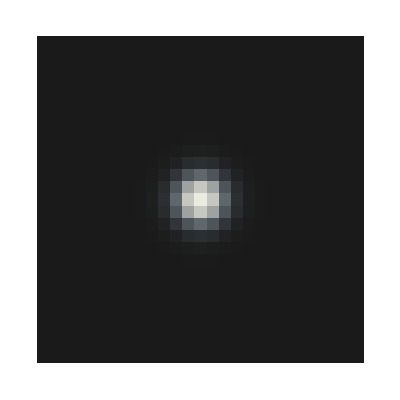

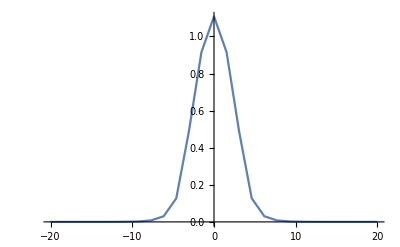

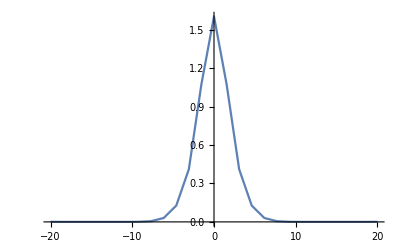

```mathematica
ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"GrayTones"]

ListPlot[Abs[Beam[[(N0+1)/2]]^2],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
ListPlot[Abs[RotateRight[Abs[Fourier[Beam]],{(N0-1)/2,(N0-1)/2}][[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{All,All}]
```

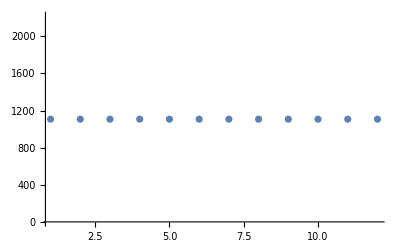

1107.14

```mathematica
ListPlot[finξ,PlotRange->All]
ξ
```

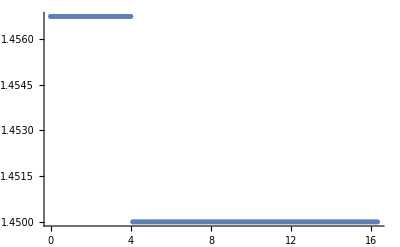

{1.45348-8.88516×10^-9 ⅈ,1.45026-0.0019913 ⅈ}

```mathematica
(*решение задачи на собственные значения (через дискретизацию)*)
λ=1.55;
k0=2Pi/λ;
NN=201;
h=CalcWindow/NN;
Clear[imn1]
RIP=Array[n[#*CalcWindow/NN]/.imn1->0&,NN];
ListPlot[RIP, DataRange->{0,CalcWindow}]
l=0;
D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];
D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];
DivByr=Array[1/h/#&,NN];
shturmop=D2/h^2+1/h D1 DivByr-l^2DivByr^2 IdentityMatrix[NN]+k0^2 RIP^2 IdentityMatrix[NN];
{β,Modes}=Eigensystem[shturmop];
β=Sqrt[β];
TrueModesNEff=Chop[Select[β/k0,((Re[#]>nMat)&&(Re[#]<nMax)&&(Im[#]<10^-10))&] ]
svect=Chop@Table[First[NullSpace[shturmop-(TrueModesNEff[[i]]*k0)^2*IdentityMatrix[NN]]],{i,Length[TrueModesNEff]}];
```

```mathematica
βRes={};
att=100;(*коэффициент, показывающий во сколько раз допустимо отличие по интенсивности*)
maxDer=100;
For[i=1,i<Length[svect],i++,
(*производная*)
dE=ListCorrelate[{-1,1},svect[[i]]];
dE=Insert[dE,svect[[i]][[-1]]-svect[[i]][[-2]],-1];
dE=dE/h;

If[MatchQ[Max[Abs[svect[[i]]^2]]/att-Abs[svect[[i]][[-5;;-1]]^2],{__?Positive}]&& MatchQ[Max[Abs[dE]]/maxDer-dE[[-5;;-1]],{__?Positive}],
βRes=Insert[βRes,TrueModesNEff[[i]],-1];
]
]
numbers=Table[Position[Re[β/k0],βRes[[i]]][[1]],{i,Length[βRes]}]
```

{}

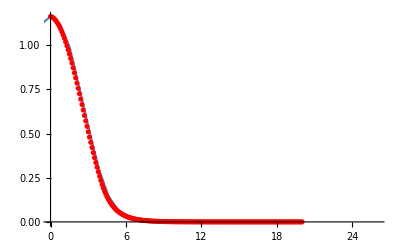

```mathematica
Show[ListPlot[Abs[Beam[[(N0+1)/2]]^2],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{0,(N0-1)/2},All}],ListPlot[Max[Abs[Beam[[(N0+1)/2]]^2]]/Max[Abs[Modes[[146]]^2]]Abs[Modes[[146]]^2],PlotRange->All,DataRange->{0,CalcWindow},PlotStyle->Red]]
```

```mathematica
(*Функция аподизации*)
```

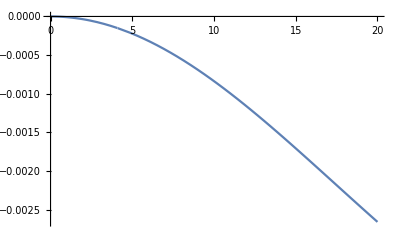

```mathematica
imn1=0.0055 ;
n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],0≤r<dCore/2},{Sqrt[nMat^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],dCore/2≤r<2dCore},{Sqrt[nMat^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],2dCore≤r}}];
Plot[Im[(n[r])^2],{r,0,CalcWindow}]
```

AppendTo::rvalue: finξ is not a variable with a value, so its value cannot be changed.

2391.07

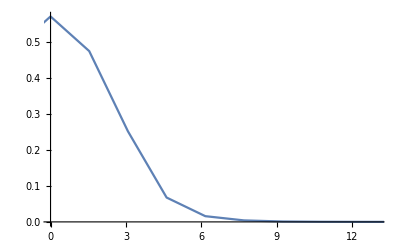

```mathematica
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[I/β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];

Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
PrevBeam=Abs[Beam[[(N0+1)/2]]];
CurBeam=Abs[Beam[[(N0+1)/2]]];
Clear[par];
CritPar=0.01;
par={};
L=10000 h;
RepPoint=100;(*промежуток, между которыми сравниваются решения, в величинах h*)
Monitor[
For[ξ=0.5h,ξ<L,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];
If[Mod[Ceiling[ξ/h-0.5],RepPoint]==0&&ξ>50h,
{
PrevBeam=CurBeam;
CurBeam=Abs[Beam[[(N0+1)/2]]];
par=AppendTo[par,NIntegrate[Abs[Interpolation[PrevBeam,InterpolationOrder->3][x]-Interpolation[CurBeam,InterpolationOrder->3][x]],{x,1,N0}]/NIntegrate[Interpolation[PrevBeam,InterpolationOrder->3][x],{x,1,N0}]];
If[Dimensions[par][[1]]>1,
If[par[[-1]]<CritPar&&par[[-2]]<CritPar,Break[]]];
}
];
],{ξ,ListPlot[Abs[Beam[[(N0+1)/2]]],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{ {-CalcWindow,CalcWindow},All},ImageSize->Large]}];
AppendTo[finξ,ξ];
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];
ξ
ListPlot[Abs[Beam[[(N0+1)/2]]^2],Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{0,(N0-1)/2},All}]
```

```mathematica
(*Гауссов пучок в среде*)
```

$Aborted

169.383

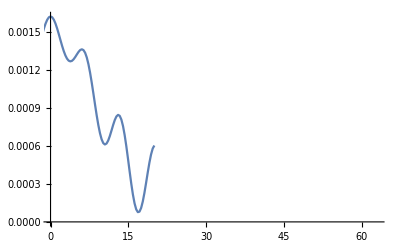

```mathematica
nMat=1;NA=0;k0=2Pi/λ;
N0=127;
imn1=0.0055 ;L=200;
n[r_]:=Piecewise[{{Sqrt[nMat^2+NA^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],0≤r<dCore/2},{Sqrt[nMat^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],dCore/2≤r<2dCore},{Sqrt[nMat^2-imn1*(1-Exp[-r^2/(3*dCore)^2])*I],2dCore≤r}}];
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-nMat^2) h];

zR=π*(dCore/2)^2/λ;
w[z_]:=dCore/2*Sqrt[1+(z/zR)^2];
intGauss[z_,r_]:=1/(π*w[z]^2/2)*Exp[-2*r^2/w[z]^2];

D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp[a_]:=Exp[-I/k0/2 D2Fourier z]/.z->a;


r2=Array[(#1^2+#2^2)&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
Beam=Sqrt[1/(π*(dCore/2)^2/2)*Exp[-2*r2/(dCore/2)^2]];
FourierOp[a_]:=Exp[-I/k0/2 D2Fourier z]/.z->a;

Monitor[
For[ξ=0.5h,ξ<L,ξ+=h,
{Beam=SpatialOp*InverseFourier[Fourier[Beam]*FourierOp[h]];
Pause[0.1];
};
],
{ξ,Show[ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{ {-CalcWindow,CalcWindow},All},ImageSize->Large],Plot[intGauss[ξ,r],{r,-CalcWindow,CalcWindow},PlotRange->All]]}]
ξ
ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{{0,(N0-1)/2},All}]
```

```mathematica
(*2*)
```

```mathematica
Clear["Global`*"]
```

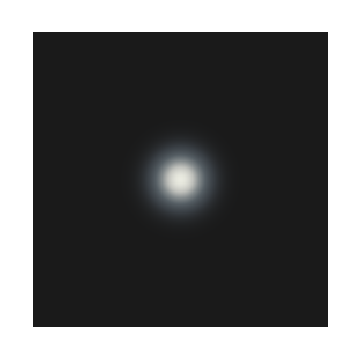

```mathematica
dCore=500;
λ=1.55;
N0=255;
CalcWindow=1000;
k0=2π/λ;
f=10000;
r2=Array[(#1^2+#2^2)&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
Beam=Exp[-r2/(dCore/2)^2];
thinLensOp=Exp[-2π I/λ*r2/2/f];
D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp[a_]:=Exp[-I/k0/2 D2Fourier z]/.z->a;
ArrayPlot[D2Fourier,DataRange->All,ColorFunction->"GrayTones"];
ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
ArrayPlot[Abs[Fourier[Beam]]^2,DataRange->All,ColorFunction->"GrayTones"];
(*радиус пучка в перетяжке после линзы = BPP(2f)/D, Db- диаметр пучка на входе*)
Manipulate[ArrayPlot[Abs[InverseFourier[Fourier[thinLensOp*InverseFourier[Fourier[Beam]*FourierOp[b*f]]]*FourierOp[a*f]]]^2,ColorFunction->"GrayTones",ImageSize->Medium],{{a,1},1/2,1.5},{{b,1},0,1.5}];
```

```mathematica
AfterLens=Fourier[thinLensOp*Beam];
Foc1[a_]:=Interpolation[Transpose[{Array[#&,N0,{-CalcWindow,CalcWindow}],Abs[InverseFourier[AfterLens*FourierOp[a*f]]][[(N0+1)/2]]^2}],InterpolationOrder->3];
w1[a_]:=2*Sqrt[NIntegrate[r*r*Evaluate[Foc1[a][r]],{r,-CalcWindow,CalcWindow}]/NIntegrate[Evaluate[Foc1[a][r]],{r,-CalcWindow,CalcWindow}]]
```

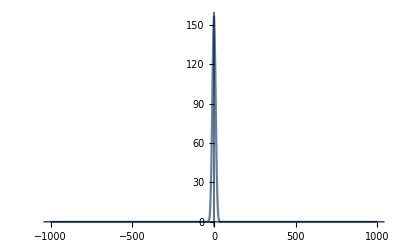

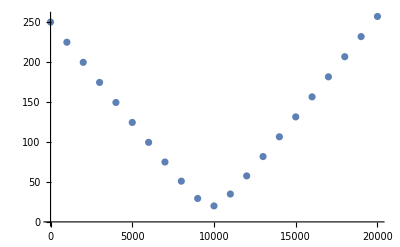

```mathematica
Plot[Evaluate[Foc1[1][r]],{r,-CalcWindow,CalcWindow},PlotRange->All]
ListPlot[Table[w1[a],{a,0,2,1/10}],DataRange->{0,2*f}]
```

```mathematica
(*3*)
Clear["Global`*"]
(*DER=0.5;
RMS=0.25;
PP=0.7;
fr[x_]:=RandomReal[{-x,x}];
ranMass:=Function[{mode,crit,pder,n},
Which[
mode=="RMS",
{m={};
AppendTo[m,fr[crit]];
For[i=2,i<=n,i++,AppendTo[m,m[[i-1]]+fr[pder]];];
rms0=Sqrt[Total[(m-Total[m]/n)^2]/n];
m=crit/rms0*m},
mode=="PP",
{m={};
AppendTo[m,fr[PP]];
For[i=2,i<=n,i++,AppendTo[m,m[[i-1]]+fr[pder]];];
m=crit/Max[Abs[m]]*m
}
]
];*)
DER=0.5;
RMS=0.25;
PP=0.7;
fr[x_]:=RandomVariate[NormalDistribution[0,x],1][[1]];
ranMass:=Function[{mode,crit,pder,n},
Which[
mode=="RMS",
{m={};
AppendTo[m,fr[crit]];
For[i=2,i<=n,i++,
tmp=m[[i-1]]+pder*10;
While[Abs[tmp-m[[i-1]]]>pder,tmp=fr[1.45*crit]];
AppendTo[m,tmp];
];
rms0=RootMeanSquare[m];
m=crit/rms0*m
},
mode=="PP",
{m={};
AppendTo[m,RandomReal[{-crit,crit}]];
For[i=2,i<=n,i++,
tmp=m[[i-1]]+pder*10;
While[Abs[tmp-m[[i-1]]]>pder,tmp=RandomReal[{-crit,crit}]];
AppendTo[m,tmp];
];
m}
]
];
```

{1024}

10.

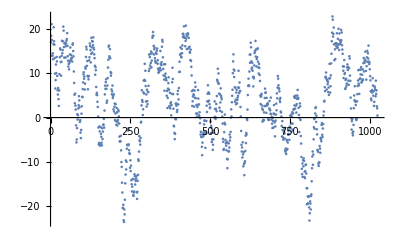

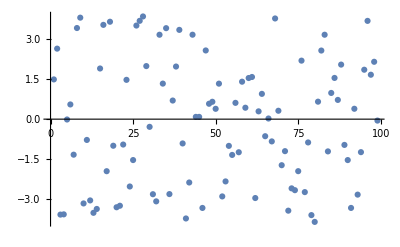

```mathematica
(*ListPlot[ranMass["RMS",2,0.04,100],Joined->True]*)
g=ranMass["RMS",10,5,1024][[1]];
Dimensions[g]
rms0=RootMeanSquare[g]
ListPlot[g]
ListPlot[g[[2;;100]]-g[[1;;99]]]
```

```mathematica
(*4*)
```

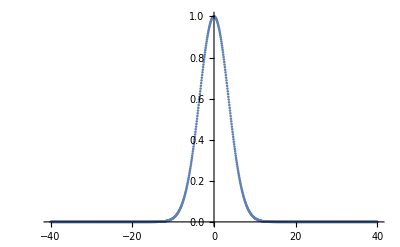

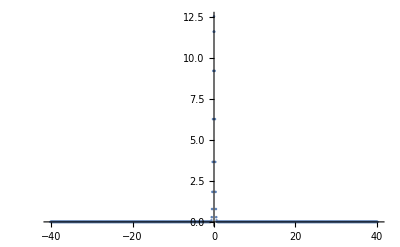

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {0.312298}. NIntegrate obtained 0.251996 and 0.0000354962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {-0.314793}. NIntegrate obtained 6.28755 and 0.000299949 for the integral and error estimates.

1.00098

```mathematica
(*Здесь расстояние будет измеряться в мм*)
rAp=40;
NN=1023;
λ=1.55*10^-3;
k0=2π/λ;
beamGauss=Array[Exp[-#^2/5^2]&,NN,{-rAp,rAp}];
kn=(π/rAp)*Array[#&,NN,{-(NN-1)/2,(NN-1)/2}];
ListPlot[beamGauss,PlotRange->All,DataRange->{-rAp,rAp}]
intFoc=Transpose[{kn,RotateLeft[Abs[Fourier[beamGauss]^2],(NN+1)/2]}];
ListPlot[intFoc,PlotRange->All]
intIntFoc=Interpolation[intFoc,InterpolationOrder->3];
θ=2/k0*Sqrt[NIntegrate[k*k*intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]/NIntegrate[intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]];
Foc=Interpolation[Transpose[{Array[#&,NN,{-rAp,rAp}],Abs[beamGauss^2]}],InterpolationOrder->3];
w=2*Sqrt[NIntegrate[r*r*Foc[r],{r,-rAp,rAp}]/NIntegrate[Foc[r],{r,-rAp,rAp}]];
M2=w*θ/(λ/π)
```

```mathematica
(*строим гистограмму*)
```

```mathematica
rAp=40;
NN=127;
λ=1.55*10^-3;
k0=2π/λ;
beamGauss=Array[Exp[-#^2/5^2]&,NN,{-rAp,rAp}];
kn=(π/rAp)*Array[#&,NN,{-(NN-1)/2,(NN-1)/2}];

Foc=Interpolation[Transpose[{Array[#&,NN,{-rAp,rAp}],Abs[beamGauss]^2}],InterpolationOrder->3];
w=2*Sqrt[NIntegrate[r*r*Foc[r],{r,-rAp,rAp}]/NIntegrate[Foc[r],{r,-rAp,rAp}]];

M2={};

DER=2;
RMS=1.;
PP=5;

For[counter=1,counter≤50,counter++,
{(*intFoc=Transpose[{kn,RotateLeft[Abs[Fourier[beamGauss*Exp[I*ranMass["RMS",RMS,DER,NN]][[1]]]]^2,(NN-1)/2]}];
intIntFoc=Interpolation[intFoc,InterpolationOrder->3];
ksr=NIntegrate[k*intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]/NIntegrate[intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}];
θRMS=2/k0*Sqrt[NIntegrate[(k-ksr)^2*intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]/NIntegrate[intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]];*)

intFoc=Transpose[{kn,RotateLeft[Abs[Fourier[beamGauss*Exp[I*ranMass["PP",PP,DER,NN]][[1]]]]^2,(NN-1)/2]}];
intIntFoc=Interpolation[intFoc,InterpolationOrder->3];
ksr=NIntegrate[k*intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]/NIntegrate[intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}];
θPP=2/k0*Sqrt[NIntegrate[(k-ksr)^2*intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]/NIntegrate[intIntFoc[k],{k,-π/rAp*(NN-1)/2,π/rAp*(NN-1)/2}]];

AppendTo[M2,{(*{12,w*θRMS/(λ/π)},*){13,w*θPP/(λ/π)}}];}
]
Histogram3D[Flatten[M2,1]]
Flatten[M2,1]
```

-Graphics3D-

{{13,7.48203},{13,8.2144},{13,8.71982},{13,7.88201},{13,10.8128},{13,9.02907},{13,10.6353},{13,8.27619},{13,10.872},{13,10.5372},{13,9.07925},{13,10.4369},{13,8.69879},{13,7.25002},{13,9.84028},{13,11.1713},{13,11.7054},{13,9.76242},{13,10.96},{13,8.53488},{13,9.7649},{13,9.89754},{13,10.5496},{13,11.9143},{13,10.2332},{13,8.15535},{13,6.20908},{13,11.598},{13,9.79925},{13,9.19664},{13,7.46497},{13,11.1409},{13,12.7528},{13,11.8423},{13,8.68703},{13,10.7648},{13,8.83736},{13,10.904},{13,9.67051},{13,9.11459},{13,8.4274},{13,10.3935},{13,10.4689},{13,9.03479},{13,8.51935},{13,8.77491},{13,10.7093},{13,8.46906},{13,11.0787},{13,9.39224}}

```mathematica
(*5*)
```

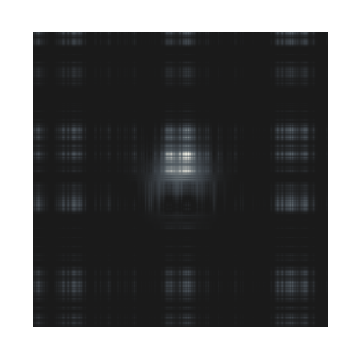

```mathematica
dCore=500;
λ=1.55;
N0=255;
CalcWindow=1000;
k0=2π/λ;
f=10000;
r2=Array[(#1^2+#2^2)&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
Beam=Exp[-r2/(dCore/2)^2]*Exp[I*TensorProduct[Flatten[ranMass["PP",1,0.2,N0]],Flatten[ranMass["PP",1,0.2,N0]]]]+TensorProduct[Flatten[ranMass["PP",1,0.2,N0]],Flatten[ranMass["PP",1,0.2,N0]]];
thinLensOp=Exp[2π I/λ*r2/2/f];
pinhole=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(*16Pi^2/(dCore/2)*)50^2},{0,(*16Pi^2/(dCore/2)*)50^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
D2Fourier=(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp[a_]:=Exp[-I/k0/2 D2Fourier z]/.z->a;
ArrayPlot[D2Fourier,DataRange->All,ColorFunction->"GrayTones"];
ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"GrayTones",ImageSize->Medium]
ArrayPlot[Abs[Fourier[Beam]]^2,DataRange->All,ColorFunction->"GrayTones"];
(*радиус пучка в перетяжке после линзы = BPP(2f)/D, D- диаметр пучка на входе*)
```

-Graphics-

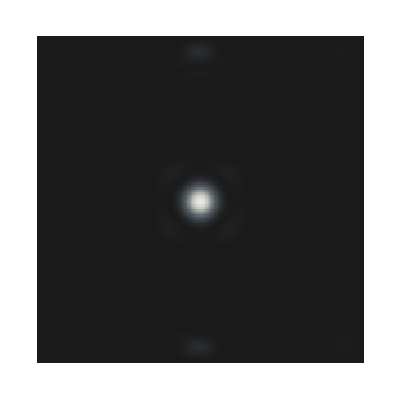

```mathematica
BeamPin=InverseFourier[Fourier[thinLensOp*Beam]*FourierOp[f]]pinhole;
ArrayPlot[Abs[BeamPin]^2]
ArrayPlot[Abs[InverseFourier[Fourier[BeamPin]*FourierOp[f]]*thinLensOp]^2,DataRange->All,ColorFunction->"GrayTones"]
```

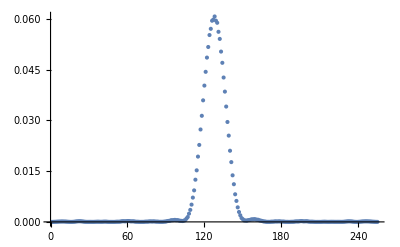

```mathematica
ListPlot[(Abs[InverseFourier[Fourier[BeamPin]*FourierOp[f]]*thinLensOp]^2)[[(N0+1)/2]],PlotRange->All]
```

```mathematica
beamGauss=Array[Exp[-#^2/2.5^2]&,NN,{-rAp,rAp}];
Foc=Interpolation[Transpose[{Array[#&,NN,{-rAp,rAp}],Abs[beamGauss]^2}],InterpolationOrder->3];
w=2*Sqrt[NIntegrate[r*r*Foc[r],{r,-rAp,rAp}]/NIntegrate[Foc[r],{r,-rAp,rAp}]]
```

2.5